```mathematica
ymc=183*10^9;(*Elastic modulus in compression*)
ymt=210*10^9;(*Elastic modulus in tension*)
sm=82*10^9;(*Shear modulus*)
pr=0.28;(*Poisson ratio*)
N[ymt/(2sm)-1];(*CORRECT! pr computed with formula: https://en.wikipedia.org/wiki/Lam%C3%A9_parameters *)
Solve[{(yy*nu)/((1+nu)(1-2nu))==lambda,yy/(2(1+nu))==mu}, {yy, nu}];(*CORRECT!*)
l1 =(ymt*pr)/((1+pr)(1-2pr));(*lambda*)
l2=ymt/(2(1+pr));(*mu, shear modulus CORRECT!!!*)
thickness=1.5;
radius=8;
start= 0.00000001;
pressure=7.*10^4;
hthickness=0.0038;
ϵ=((1-pr^2)*radius*pressure)/(ymt*hthickness)
ν=pr

σx=6.4;
σy=4.4;(*approximate beamspot y exp(-x^2/(2 σy^2))*)
beamfunc[x_,y_] = E^(-(x^2/(2 σx^2)+y^2/(2 σy^2)));
beamfuncpolar[ρ_,θ_] = E^(-((ρ^2 Cos[θ]^2)/(2 σx^2)+(ρ^2 Sin[θ]^2)/(2 σy^2)));
```

0.000646737

0.28

```mathematica
(*Solve equations*)
eq1=ρ/1 D[ρ((D[r2[ρ],ρ])+(ν r2[ρ])/1+1/2 ρ(D[z1[ρ], ρ])^2), ρ]-ν/1 ρ(D[r2[ρ],ρ]+1/2(D[z1[ρ], ρ])^2)-r2[ρ]/1==0//Simplify;
eq2=1/1 D[1(D[z1[ρ], ρ])(D[r2[ρ],ρ]ρ+ν r2[ρ]/1+1/2(D[z1[ρ], ρ])^2 ρ), ρ]==-ρ//Simplify;
s=NDSolve[{eq1, eq2, r2[1]==0,z1[1]==0,(D[z1[ρ], ρ]/.ρ->0)==0 , r2[start]==0},{r2, z1},{ρ,start,1}];
```

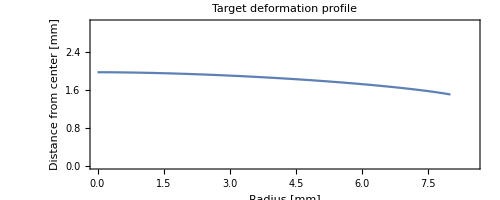

```mathematica
(*Plot deformation*)
expr0 [ρ_]= {radius*(ρ+ϵ^(2/3) r2[ρ]),radius*(ϵ^(1/3)z1[ρ])+thickness};
plt1= ParametricPlot[{Evaluate[expr0[ρ]/.s]}, {ρ, start, 1}, PlotRange->{{0, 8.5},{0, 3}}];
Show[plt1,Frame->True, FrameLabel->{"Radius [mm]","Distance from center [mm]"}, PlotLabel->HoldForm[Target deformation profile],LabelStyle->{GrayLevel[0]}, PlotTheme->"Minimal"]
(*ParametricPlot[{Evaluate[{radius*(1+ϵ^(2/3)r2'[ρ]),radius*(ϵ^(1/3)z1'[ρ])}/.s]}, {ρ, start, 1}, PlotRange->Full]*)
(*ParametricPlot[Evaluate[r2[ρ], z1[ρ]]/.s, {ρ, 0.1, 1}]*)
```

```mathematica
(*Compute average beam thickness to pass target*)
(*ListPointPlot3D[ParallelTable[beamfunc[x, y, σx, σy], {x, -10, 10, 0.1}, {y, -10, 10, 0.1}]]*)
(*NIntegrate[beamfuncpolar[ρ, θ]*Evaluate[expr0[ρ]/.s*Sin[θ]]*)
fun=Interpolation[ParallelTable[expr0 [ρ]/.s[[1]], {ρ, start, 1, 0.05}]];
liminf=0.001;
limsup=7.9;

NIntegrate[1/NIntegrate[beamfuncpolar[ρ, θ]*Sin[θ], {ρ, liminf, limsup}, {θ, 0, π}]*beamfuncpolar[ρ, θ]*Sin[θ]*(2*fun[ρ]), {ρ, liminf, limsup}, {θ, 0, π}](*mean thickness*)
Export["He_thickness_700mbar_euc.txt",Table[{{ρ, Evaluate[fun[ρ]]}}, {ρ, start, 8.0, 0.01}]](*deformation in cartesian coordinates*)
Export["He_thickness_derivative_700mbar_euc.txt",Table[{{ρ, Evaluate[fun'[ρ]]}}, {ρ, start, 8.0, 0.01}]](*deformation in cartesian coordinates*)
```

3.72109

InterpolatingFunction::dmval: Input value {7.61} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

He_thickness_700mbar_euc.txt

InterpolatingFunction::dmval: Input value {7.61} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

He_thickness_derivative_700mbar_euc.txt

```mathematica
(*thickness as a function of angle from normal*)
expr1 = {ArcTan[radius*(ρ+ϵ^(2/3) r2[ρ])/(radius*(ϵ^(1/3)z1[ρ])+thickness)],√((radius*(ρ+ϵ^(2/3) r2[ρ]))^2+(radius*(ϵ^(1/3)z1[ρ])+thickness)^2)};
p1 = ParametricPlot[{Evaluate[expr1/.s]}, {ρ, start, 1}, PlotRange->{{0, 3},{1,10 }}];
p2 = Plot[thickness/Cos[θ], {θ, 0, 1.5}, PlotStyle->Red];
plt2 = Show[p1, p2];
Show[plt2,Frame->True, FrameLabel->{"Angle [rad]","Thickness [mm]"}, PlotLabel->HoldForm[Effective thickness],LabelStyle->{GrayLevel[0]}, PlotTheme->"Minimal"]
Export["He_thickness_700mbar.txt",Table[Evaluate[expr1/.s], {ρ, start, 2.0, 0.001}]]
```

```mathematica
(*havar entrance angle as a function of angle from normal*)
expr2 = {ArcTan[radius*(ρ+ϵ^(2/3) r2[ρ])/(radius*(ϵ^(1/3)z1[ρ])+thickness)],π/2-ArcCos[((radius*(ρ+ϵ^(2/3) r2[ρ])*radius*(1+ϵ^(2/3) D[r2[ρ], ρ])+(radius*(ϵ^(1/3)z1[ρ])+thickness)*radius*(ϵ^(1/3)D[z1[ρ], ρ]))/(√((radius*(ρ+ϵ^(2/3) r2[ρ]))^2+(radius*(ϵ^(1/3)z1[ρ])+thickness)^2)*√((radius*(1+ϵ^(2/3) D[r2[ρ], ρ]))^2+(radius*(ϵ^(1/3)D[z1[ρ], ρ]))^2)))]};
p3 = ParametricPlot[{Evaluate[expr2/.s]}, {ρ, start, 1}, PlotRange->{{0, 1.5},{0,1.2}}];
p4 = Plot[θ, {θ, 0, 1.5}, PlotStyle->Red];
plt3 = Show[p3, p4];
Show[plt3,Frame->True, FrameLabel->{"Angle [rad]","Entrance angle [rad]"}, PlotLabel->HoldForm[Entrance angle in HAVAR],LabelStyle->{GrayLevel[0]}, PlotTheme->"Minimal"]
Export["Entrance_angle_700mbar.txt",Table[Evaluate[expr2/.s], {ρ, start, 1.5, 0.001}]]
```